```mathematica
(*  Guy F. Mongelli                               ChE 400
   Prof. Clark                                   9/26/2010     *)
```

```mathematica
(*  Assignment #5 *)
```

```mathematica
(* Problem #1  *)
(* Developing a fourier sine series that approximates the initial condition.  This codfe is taken from the workbook developed for Assignment #4, Problem 1, part B  *)
```

```mathematica
(* Part B *)
```

```mathematica
(* Now consider the Fourier Sine Series for F.  The Fourier Sine Series is the periodic extension of the odd extension of x. *)
```

```mathematica
T0=100 (* deg C *);
a=2;
b=1;
L=a;
fbas[x_]:=4*T0(x/a)(1-x/a);
```

```mathematica
fbasod[x_]:=If[(x≥0),fbas[x],fbas[-x]];
fod[x_]:=fbasod[Mod[x,2*L,-L]];
```

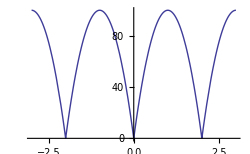

```mathematica
graphoneFSine=Plot[fod[x],{x,-3,3}]
```

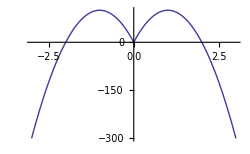

```mathematica
Plot[fbasod[x],{x,-3,3}]
```

```mathematica
(* The odd extended function is discontinuous every 2L period.  Therefore, the periodic extension of the odd extension will have foruier coefficients that drop of as 1/n.  *)
```

```mathematica
aFSine[0]=1/(2L)∫_-L^L fod[x]ⅆx
```

200/3

```mathematica
aFSine[n_]=Simplify[1/L∫_-L^L fod[x]Cos[(n π x)/L]ⅆx,n∈Integers]
```

-(800 (1+(-1)^n))/(n^2 π^2)

```mathematica
bFSine[n_]=Simplify[(2*T0)/Cosh[(n π b)/a]∫_-L^L fod[x]Sin[(n π x)/L]ⅆx,n∈Integers]
```

0

```mathematica
coeffsFSine=Table[{aFSine[i],bFSine[i]},{i,1,20}];
TableForm[coeffsFSine]
```

0 | 0
-400/π^2 | 0
0 | 0
-100/π^2 | 0
0 | 0
-400/(9 π^2) | 0
0 | 0
-25/π^2 | 0
0 | 0
-16/π^2 | 0
0 | 0
-100/(9 π^2) | 0
0 | 0
-400/(49 π^2) | 0
0 | 0
-25/(4 π^2) | 0
0 | 0
-400/(81 π^2) | 0
0 | 0
-4/π^2 | 0

```mathematica
FxComp[k_,x_]:=coeffsFSine[[k,1]]*Cos[k*Pi*x/L]
```

```mathematica
FyComp[k_,y_]:=(8*T0)/π^3 1/(2k+1)^3 Cosh[(2k+1)π y/a]/Cosh[(2k+1)π b/a]
```

```mathematica
Fx[k_,x_,y_]:=FxComp[k,x]*FyComp[k,y]
```

```mathematica
FSum[N_,x_,y_]:=aFSine[0]+∑_(k=1)^N Fx[k,x,y]
```

```mathematica
FSum[5,x,y]
```

-(2560 Cos[π x] Cosh[(5 π y)/2] Sech[(5 π)/2])/π^5-(80000 Cos[2 π x] Cosh[(9 π y)/2] Sech[(9 π)/2])/(729 π^5)

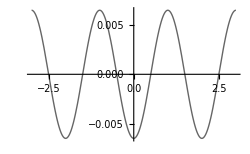

```mathematica
graphtwoFSine=Plot[FSum[5,x,0],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

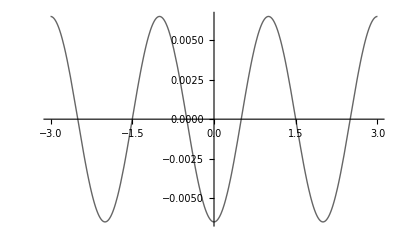

```mathematica
bothtwoFSine=Show[graphtwoFSine,graphoneFSine]
```

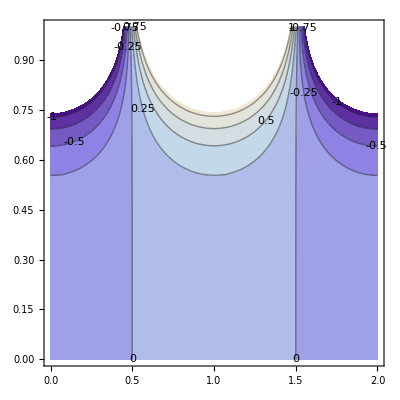

```mathematica
ContourPlot[FSum[10,x,y],{x,0,a},{y,0,b},ContourLabels->True]
```

```mathematica
(* Problem 2   *)
```

```mathematica
Clear[a,b,c,d,λ,F,Fn]
```

```mathematica
a=1;
b=2;
```

```mathematica
F[x_]:=(c*Cosh[(1+λ)^(1/2)*x]+d*Sinh[(1+λ)^(1/2)*x])
```

```mathematica
F[x]
```

c Cosh[x √(1+λ)]+d Sinh[x √(1+λ)]

```mathematica
D[F[x],x]
```

d √(1+λ) Cosh[x √(1+λ)]+c √(1+λ) Sinh[x √(1+λ)]

```mathematica
F'[0]
```

d √(1+λ)

```mathematica
Solve[{F'[0]==0,F[1]== 1},{c,d}]
```

{{c→Sech[√(1+λ)],d→0}}

```mathematica
c=Sech[√(1+λ[n])];
d=0;
```

```mathematica
λ[n_]:=(n^2 π^2)/b^2
```

```mathematica
Fn[x_,n_]=(c*Cosh[(1+λ[n])^(1/2)*x]+d*Sinh[(1+λ[n])^(1/2)*x])
```

Cosh[√(1+(n^2 π^2)/4) x] Sech[√(1+(n^2 π^2)/4)]

```mathematica
G[y_]:=e*Sin[(n π y)/b]+f*Cos[(n π y)/b]
```

```mathematica
Clear[e,f]
```

```mathematica
Solve[{G[0]==0,G[1]==1},{e,f}]
```

{{e→Csc[(n π)/2],f→0}}

```mathematica
e=Csc[(n π)/2];
f=0;
```

```mathematica
G[y]
```

Csc[(n π)/2] Sin[(n π y)/2]

```mathematica
Φ[x_,y_,N_]:=∑_(n=1)^N Fn[x,n]*G[y]
```

```mathematica
Φ[x,y,1]
```

Cosh[√(1+π^2/4) x] Sech[√(1+π^2/4)] Sin[(π y)/2]

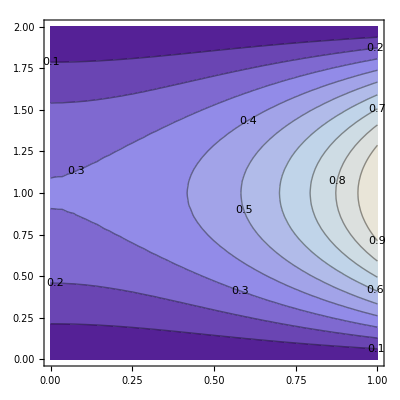

```mathematica
ContourPlot[Φ[x,y,1],{x,0,a},{y,0,b},ContourLabels->True]
```

```mathematica
fbas[x]:=1
```

```mathematica
fbasod[x_]:=If[(x≥0),fbas[x],-fbas[-x]];
fod[x_]:=fbasod[Mod[x,2*L,-L]];
```

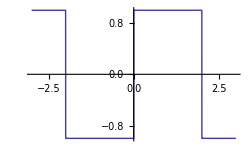

```mathematica
graphoneFSine=Plot[fod[x],{x,-3,3}]
```

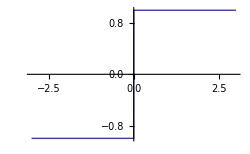

```mathematica
Plot[fbasod[x],{x,-3,3}]
```

```mathematica
aFSine[0]=1/(2 L)∫_-L^L fod[x]ⅆx
```

0

```mathematica
aFSine[n_]=Simplify[1/L∫_-L^L fod[x]Cos[(n π x)/L]ⅆx,n∈Integers]
```

0

```mathematica
bFSine[n_]=Simplify[1/L∫_-L^L fod[x]Sin[(n π x)/L]ⅆx,n∈Integers]
```

-(2 (-1+(-1)^n))/(n π)

```mathematica
coeffsFSine=Table[{aFSine[i],bFSine[i]},{i,1,20}];
TableForm[coeffsFSine]
```

0 | 4/π
0 | 0
0 | 4/(3 π)
0 | 0
0 | 4/(5 π)
0 | 0
0 | 4/(7 π)
0 | 0
0 | 4/(9 π)
0 | 0
0 | 4/(11 π)
0 | 0
0 | 4/(13 π)
0 | 0
0 | 4/(15 π)
0 | 0
0 | 4/(17 π)
0 | 0
0 | 4/(19 π)
0 | 0

```mathematica
FsSine[k_,x_]:=coeffsFSine[[k,2]]*Sin[k*Pi*x/L]+coeffsFSine[[k,1]]*Cos[k*Pi*x/L]
```

```mathematica
fourierFSine[n_,x_]:=aFSine[0]+∑_(k=1)^n FsSine[k,x]
```

```mathematica
fourierFSine[5,x]
```

(4 Sin[(π x)/2])/π+(4 Sin[(3 π x)/2])/(3 π)+(4 Sin[(5 π x)/2])/(5 π)

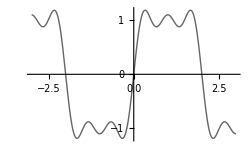

```mathematica
graphtwoFSine=Plot[fourierFSine[5,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

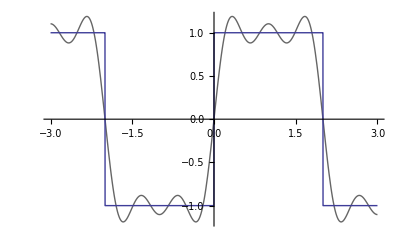

```mathematica
bothtwoFSine=Show[graphtwoFSine,graphoneFSine]
```

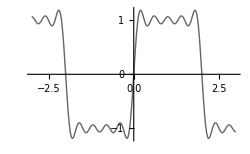

```mathematica
graphthreeFSine=Plot[fourierFSine[10,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

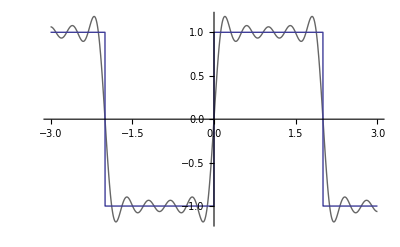

```mathematica
boththreeFSine=Show[graphthreeFSine,graphoneFSine]
```

```mathematica
graphsixFSine=Plot[fourierFSine[20,x],{x,-3,3},PlotStyle->GrayLevel[0.4]];
```

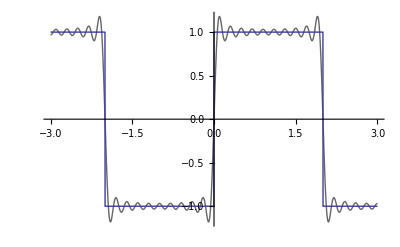

```mathematica
bothsixFSine=Show[graphsixFSine,graphoneFSine]
```

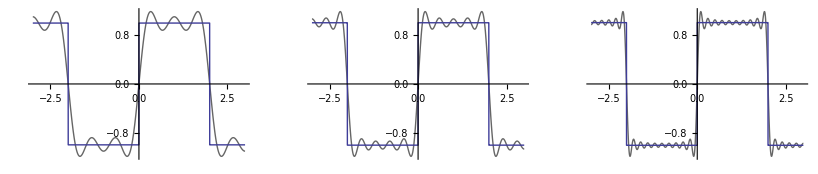

```mathematica
Show[GraphicsRow[{bothtwoFSine,boththreeFSine,bothsixFSine}]]
```

```mathematica
(* Problem #3)
```

```mathematica
Clear[An,Bn,c,g,h]
```

```mathematica
L=1;
c=1;
g=1;
h=1;
```

```mathematica
y0[x_]:=g*Sin[(π x)/L];
v0[x_]:=h*Sin[(π x)/L];
```

```mathematica
y0[x]
```

Sin[π x]

```mathematica
v0[x]
```

Sin[π x]

```mathematica
w[n_]:=(n π c)/L
```

```mathematica
An[n_]:=Simplify[2/L∫_-L^L y0[x]*Sin[(n π x)/L]ⅆx,n∈Integers]
```

```mathematica
An[1]
```

2

```mathematica
Bn[n_]:=2/(w[n]*L)Simplify[2/L∫_-L^L v0[x]*Sin[(n Pi x)/L]ⅆx,n∈Integers]
```

```mathematica
Bn[1]
```

4/π

```mathematica
y[x_,t_]=(An[1]*Cos[w[1]*t]+Bn[1]*Sin[w[1]*t])Sin[(Pi x)/L]
```

(2 Cos[π t]+(4 Sin[π t])/π) Sin[π x]

```mathematica
y[x,0]
```

2 Sin[π x]

```mathematica
An[1]
```

2

```mathematica
w[1]
```

π

```mathematica
y[L/2,0]
```

2

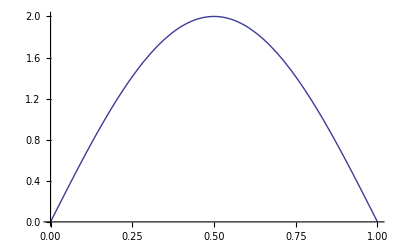

```mathematica
Plot[y[x,0],{x,0,L}]
```

```mathematica
ContourPlot
```

ContourPlot

```mathematica
g
```